# Homework 5 Plots

MATH224 Homework 5 Plots. Used this instead of HPG
Trevor Swan - tcs94
I don’t know this language too well, so this was assisted by the internet

## Section 2.1

## Question 2.1.7

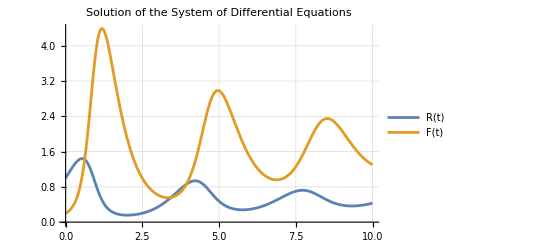

```mathematica
Clear["Global`*"]

(*Define the system of differential equations*)
eqns={R'[t]==2 (1-R[t]/3) R[t]-R[t] F[t],F'[t]==-2 F[t]+4 R[t] F[t]};

(*New initial condition*)
newInitialCondition={R[0]==1,F[0]==0.2};

(*Solve the system numerically*)
sol=NDSolve[{eqns,newInitialCondition},{R,F},{t,0,10}];

(*Plot the solution*)
Plot[Evaluate[{R[t],F[t]}/. sol],{t,0,10},PlotLegends->{"R(t)","F(t)"},FrameLabel->{"t","Value"},PlotLabel->"Solution of the System of Differential Equations",GridLines->Automatic,GridLinesStyle->LightGray,Axes->True]
```

## Section 2.2

## Question 2.2.1

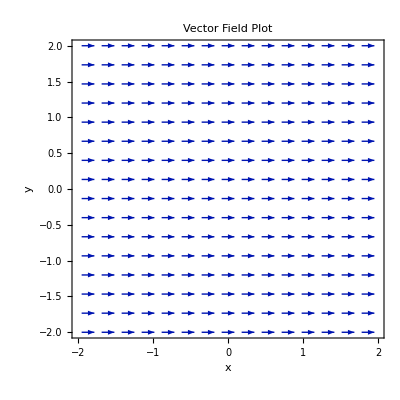

```mathematica
Clear["Global`*"]

VectorPlot[{1,0},{v,-2,2},{y,-2,2},VectorScale->{0.03,Automatic,None},VectorStyle->Arrowheads[0.02],FrameLabel->{"x","y"},PlotLabel->"Vector Field Plot"]
```

## Question 2.2.5

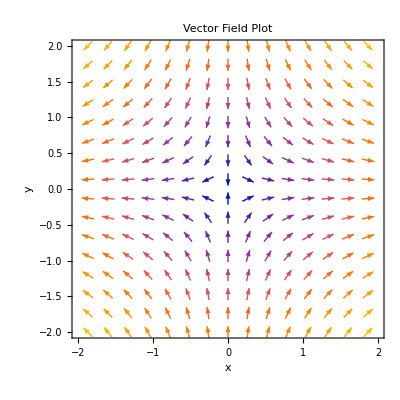

```mathematica
Clear["Global`*"]

VectorPlot[{x,-y},{x,-2,2},{y,-2,2},VectorScale->{0.03,Automatic,None},VectorStyle->Arrowheads[0.02],FrameLabel->{"x","y"},PlotLabel->"Vector Field Plot"]
```

## Question 2.2.9

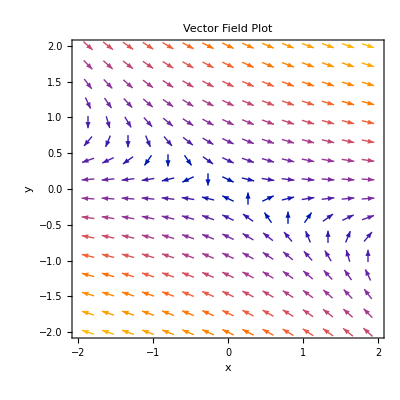

```mathematica
Clear["Global`*"]

VectorPlot[{x+2*y,-y},{x,-2,2},{y,-2,2},VectorScale->{0.03,Automatic,None},VectorStyle->Arrowheads[0.02],FrameLabel->{"x","y"},PlotLabel->"Vector Field Plot"]
```

## Section 2.3

## Question 2.3.1

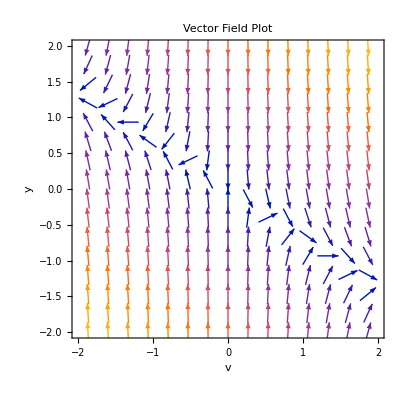

```mathematica
Clear["Global`*"]

VectorPlot[{v,-7 v-10 y},{v,-2,2},{y,-2,2},VectorScale->{0.05,Automatic,None},VectorStyle->Arrowheads[0.02],FrameLabel->{"v","y"},PlotLabel->"Vector Field Plot"]
```

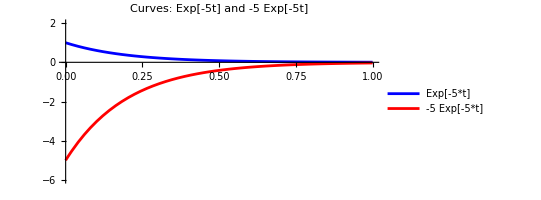

```mathematica
Plot[{Exp[-5 t],-5 Exp[-5 t]},{t,0,1},PlotStyle->{Blue,Red},PlotLegends->{"Exp[-5*t]","-5 Exp[-5*t]"},AspectRatio->0.5,FrameLabel->{"Time (t)","Function Value"},PlotLabel->"Curves: Exp[-5t] and -5 Exp[-5t]",PlotRange->{{0,1},{-6,2}}]
```

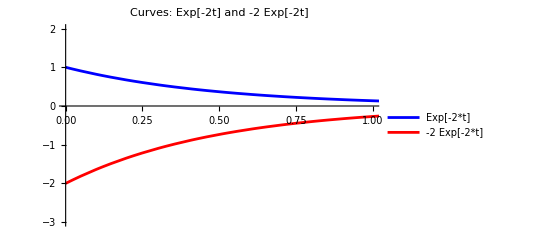

```mathematica
Plot[{Exp[-2 t],-2 Exp[-2 t]},{t,0,10},PlotStyle->{Blue,Red},PlotLegends->{"Exp[-2*t]","-2 Exp[-2*t]"},FrameLabel->{"Time (t)","Function Value"},PlotLabel->"Curves: Exp[-2t] and -2 Exp[-2t]",PlotRange->{{0,1},{-3,2}}]
```

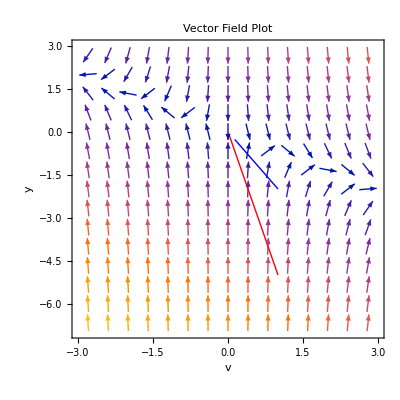

```mathematica
Clear["Global`*"]

(*Define the system of differential equations*)
eqns={v'[t]==-7 v[t]-10 y[t],y'[t]==v[t]};

(*Define the vector-valued functions*)
f[t_]:={ Exp[-5 t],-5Exp[-5 t]};
g[t_]:={Exp[-2 t],-2Exp[-2 t]};

(*Plot the vector field*)
vectorFieldPlot=VectorPlot[{v,-7 v-10 y},{v,-3,3},{y,-7,3},VectorScale->{0.03,Automatic,None},VectorStyle->Arrowheads[0.02],FrameLabel->{"v","y"},PlotLabel->"Vector Field Plot"];

(*Plot the solution curves*)
solutionCurvesPlot=ParametricPlot[{f[t],g[t]},{t,0,1},PlotStyle->{{Red,Thick},{Blue,Thick}}];

(*Show the vector field plot with solution curves*)
Show[vectorFieldPlot,solutionCurvesPlot]
```

## Question 2.3.3

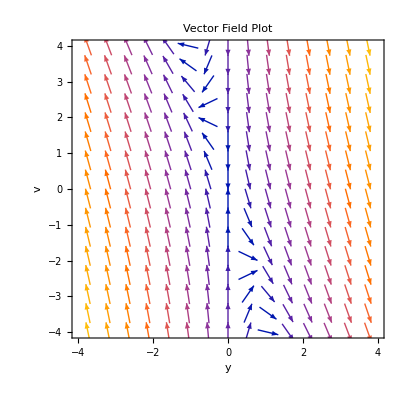

```mathematica
VectorPlot[{v,-4v- y},{v,-4,4},{y,-4,4},VectorScale->{0.05,Automatic,None},VectorStyle->Arrowheads[0.02],FrameLabel->{"y","v"},PlotLabel->"Vector Field Plot"]
```

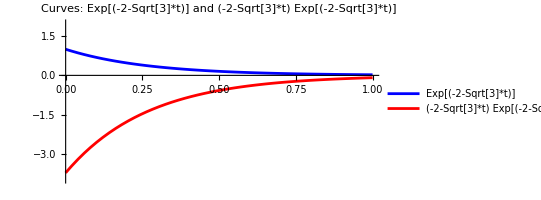

```mathematica
Plot[{Exp[(-2-Sqrt[3])*t],((-2-Sqrt[3]))*Exp[(-2-Sqrt[3])*t]},{t,0,1},PlotStyle->{Blue,Red},PlotLegends->{"Exp[(-2-Sqrt[3]*t)]","(-2-Sqrt[3]*t) Exp[(-2-Sqrt[3]*t)]"},AspectRatio->0.5,FrameLabel->{"Time (t)","Function Value"},PlotLabel->"Curves: Exp[(-2-Sqrt[3]*t)] and (-2-Sqrt[3]*t) Exp[(-2-Sqrt[3]*t)]",PlotRange->{{0,1},{-4,2}}]
```

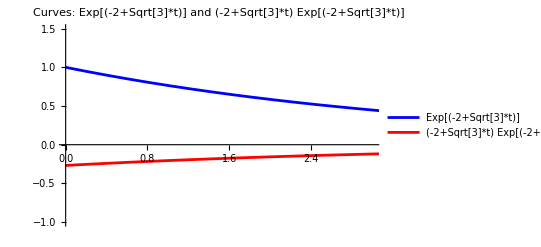

```mathematica
Plot[{Exp[(-2+Sqrt[3])*t],(-2+Sqrt[3])*Exp[(-2+Sqrt[3])*t]},{t,0,10},PlotStyle->{Blue,Red},PlotLegends->{"Exp[(-2+Sqrt[3]*t)]","(-2+Sqrt[3]*t) Exp[(-2+Sqrt[3]*t)]"},FrameLabel->{"Time (t)","Function Value"},PlotLabel->"Curves: Exp[(-2+Sqrt[3]*t)] and (-2+Sqrt[3]*t) Exp[(-2+Sqrt[3]*t)]",PlotRange->{{0,3},{-1,1.5}}]
```

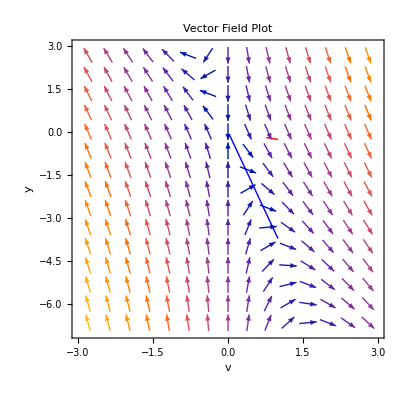

```mathematica
Clear["Global`*"]

(*Define the system of differential equations*)
eqns={v'[t]==-4v[t]-y[t],y'[t]==v[t]};

(*Define the vector-valued functions*)
f[t_]:={ Exp[(-2+Sqrt[3])*t],(-2+Sqrt[3])*Exp[(-2+Sqrt[3])*t]};
g[t_]:={Exp[(-2-Sqrt[3])*t],((-2-Sqrt[3]))*Exp[(-2-Sqrt[3])*t]};

(*Plot the vector field*)
vectorFieldPlot=VectorPlot[{v,-4v-y},{v,-3,3},{y,-7,3},VectorScale->{0.03,Automatic,None},VectorStyle->Arrowheads[0.02],FrameLabel->{"v","y"},PlotLabel->"Vector Field Plot"];

(*Plot the solution curves*)
solutionCurvesPlot=ParametricPlot[{f[t],g[t]},{t,0,1},PlotStyle->{{Red,Thick},{Blue,Thick}}];

(*Show the vector field plot with solution curves*)
Show[vectorFieldPlot,solutionCurvesPlot]
```